# Presentation Quality Graphs

RockSprings Plot

```mathematica
(*hurricane irene*)


Block[{stagesfeet,times,dates,absolutetimes},
stagesfeet=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\observed stage\\02083893.txt",0,3,3,Number];
times=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\observed stage\\02083893.txt",0,3,2,Word];
dates=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\observed stage\\02083893.txt",0,3,1,Word];
absolutetimes=Table[AbsoluteTime[StringJoin[dates[[i]]," ",times[[i]]]],{i,1,Length[times]}];
rockspringsobscatter=Transpose[Table[{absolutetimes,stagesfeet}]];
];
```

AbsoluteTime::ambig: Warning: the interpretation of the string "8/10/2011 0:30" as a date is ambiguous.

General::stop: Further output of AbsoluteTime :: ambig will be suppressed during this calculation.

```mathematica
Block[{stagesmspinup,stagesmhurricane,stagesmspindown,stagesm,start,times},
stagesmspinup=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\spinup\\rock_springs_wse_median_spinup.txt",0,1,1,Number];
stagesmhurricane=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\hurricane\\rock_springs_wse_median_hurricane.txt",0,1,1,Number];
stagesmspindown=ReadUSGSQfile["C:\\Users\\Sam\\Desktop\\Thesis Work\\irene\\spindown\\rock_springs_wse_median_spindown.txt",0,1,1,Number];


stagesm=Flatten[{stagesmspinup,stagesmhurricane,stagesmspindown}];

start=AbsoluteTime["July 6, 2011 00:00"];
times=Table[start+300*i,{i,0,Length[stagesm]-1}];


rockspringsadcircscatter=Transpose[Table[{times,stagesm*3.28084}]];

];
```

AbsoluteTime::ambig: Warning: the interpretation of the string "8/10/2011" as a date is ambiguous.

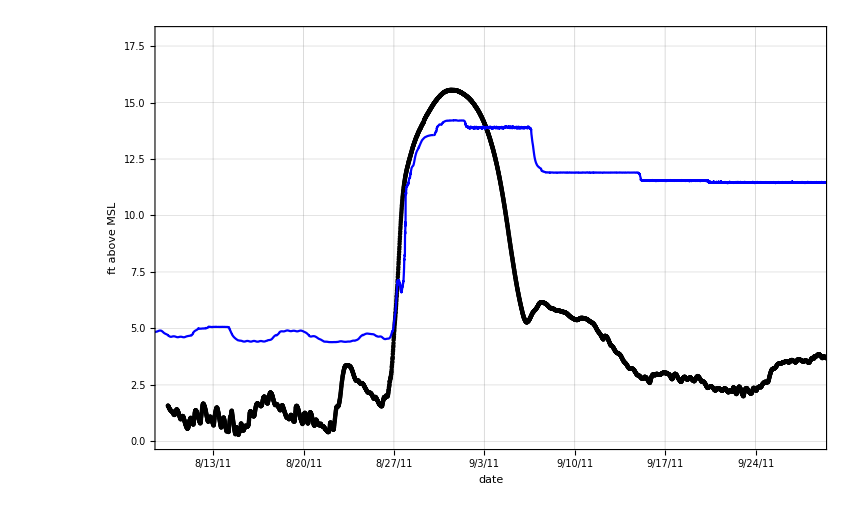

```mathematica
start=AbsoluteTime["8/10/2011"];
end=start+(24*60*60*50);

rsobs=scatterplot[rockspringsobscatter,start,end,0,18,"ft above MSL","date","Rock Springs",7,False,Black];
rsadcirc=scatterplot[rockspringsadcircscatter,start,end,0,18,"ft above MSL","date","Rock Springs",7,True,Blue];

Show[rsobs,rsadcirc]
```